## Plot of Kendall tau distributions

## Import data

```mathematica
SetDirectory["/Users/tb460/Library/Mobile Documents/com~apple~CloudDocs/Research/critical_transitions_16/may_harvest_model/additive_noise"];
```

```mathematica
ktauRaw=Import["data_export/ktau_add1.csv"];
```

```mathematica
ktauRaw[[1]]
```

{,Variance,Lag-1 AC,Smax}

## Box-whisker plots

```mathematica
(* figure parameters *)
imgs=250;
padding={{60,30},{50,40}};
aratio=0.8;
```

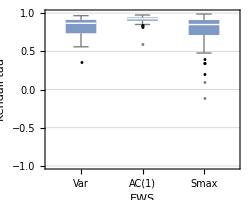

```mathematica
boxWhisker=BoxWhiskerChart[Transpose[ktauRaw[[2;;,2;;]]],"Outliers",
PlotRange->{All,{-1,1}},
FrameTicks->{{Automatic,None},{Automatic,None}},
ImageSize->imgs,
Frame->True,
LabelStyle->14,
ChartStyle->Lighter[TMBcolours[[1]],0.2],
ChartLabels->{"Var","AC(1)","Smax"},
GridLines->{None,Range[-1,1,0.5]},
ImagePadding->padding,
AspectRatio->aratio,
FrameLabel->{{"Kendall tau",None},{"EWS",None}}]
```

```mathematica
(* export figure *)
Export["figures/ktau_tshort.png",boxWhisker,ImageResolution->200];
```